## Ugeseddel 1: Simplex

## Opgave 1: plot og simplex

### (a) og (b)

```mathematica
z[x1_,x2_]:=2x1+x2
```

```mathematica
b1[x1_,x2_]:=x2
```

```mathematica
b2[x1_,x2_]:=2x1+5x2
```

```mathematica
b3[x1_,x2_]:=x1+x2
```

```mathematica
b4[x1_,x2_]:=3x1+x2
```

```mathematica
bv={10,60,18,44};
```

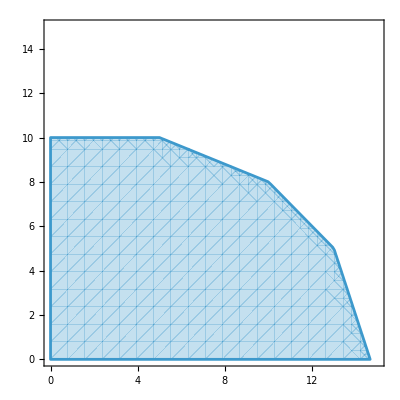

```mathematica
rp = RegionPlot[{
b1[x1,x2]<=bv[[1]]&&
b2[x1,x2]<=bv[[2]]&&
b3[x1,x2]<=bv[[3]]&&
b4[x1,x2]<=bv[[4]]
},{x1,0,15},{x2,0,15}]
```

```mathematica
ContourPlot[{
z[x1,x2]==zl,
b1[x1,x2]==bv[[1]],
b2[x1,x2]==bv[[2]],
b3[x1,x2]==bv[[3]],
b4[x1,x2]==bv[[4]]
},{x1,0,15},{x2,0,15}]
```

```mathematica
Manipulate[
Show[
rp,
ContourPlot[{
z[x1,x2]==zl,
b1[x1,x2]==bv[[1]],
b2[x1,x2]==bv[[2]],
b3[x1,x2]==bv[[3]],
b4[x1,x2]==bv[[4]]
},{x1,0,15},{x2,0,15}],PlotLegends->"Expressions"],
{zl,0,50}]
```

Show::gcomb: Could not combine the graphics objects in 
    Show[rp, -Graphics-, PlotLegends -> Expressions].

Den blå linje er objektfunktionen. Vi kan se at maximum er ved en værdi af objektfunktionen på 31. 
Her skærer bibetingelsen 3 x_1+x_2<=44 bibetingelsen x_1+x_2<=18 hinanden. Hvis vi vi løser ligningerne

3 x_1+x_2=44
x_1+x_2=18

```mathematica
Solve[{3x1+x2==44,x1+x2==18}]
```

{{x1→13,x2→5}}

Ser vi at optimum er når x_1=13 og x_2=5.

### (c)

Vi løser problemet med simplex-metoden.
Vi starter med at opstille tableauet

Derefter køres primal simplex

Det ses at vi får præcis samme løsning.

## Opgave 2: Simplex

### (a)

Her ses det ønskede tableau

Hvor der er indført en slackvariabel for hver bibetingelse.

### (b)

Vi løser problemet med simplex-metoden

Vi ser at den optimale løsning er når (x_1,x_2,x_3)=(0,10,6.67) og her bliver værdien af objektfunktionen Z=70.

## Opgave 3: plot og omskrivning af simplex (ikke løse)

### (a)

For at illustrere problemet, defineres de givne informationer

```mathematica
Clear["Global`*"]
```

```mathematica
z[x1_,x2_]:=5x1+7x2
```

```mathematica
b1[x1_,x2_]:=2x1+3x2
```

```mathematica
b2[x1_,x2_]:=3x1+4x2
```

```mathematica
b3[x1_,x2_]:=x1+x2
```

```mathematica
bv:={42,60,18}
```

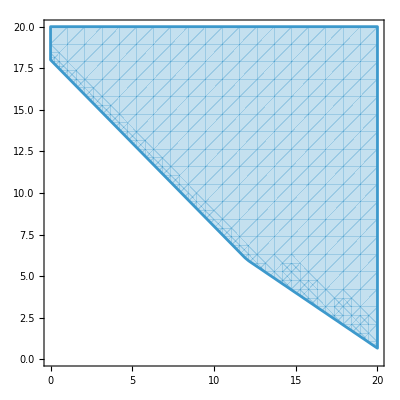

```mathematica
rp=RegionPlot[{
b1[x1,x2]>=bv[[1]]&&
b2[x1,x2]>=bv[[2]]&&
b3[x1,x2]>=bv[[3]]
},{x1,0,20},{x2,0,20}]
```

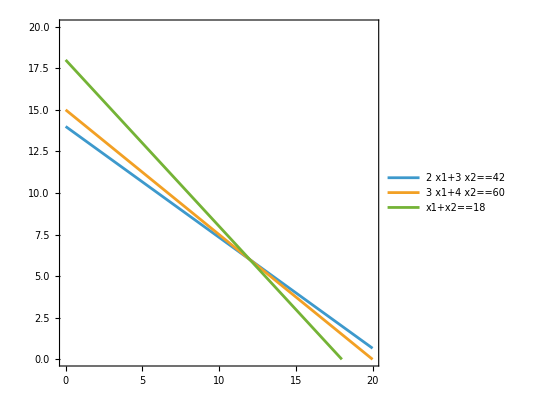

```mathematica
cp=ContourPlot[{
b1[x1,x2]==bv[[1]],
b2[x1,x2]==bv[[2]],
b3[x1,x2]==bv[[3]]
},{x1,0,20},{x2,0,20},PlotLegends->"Expressions"]
```

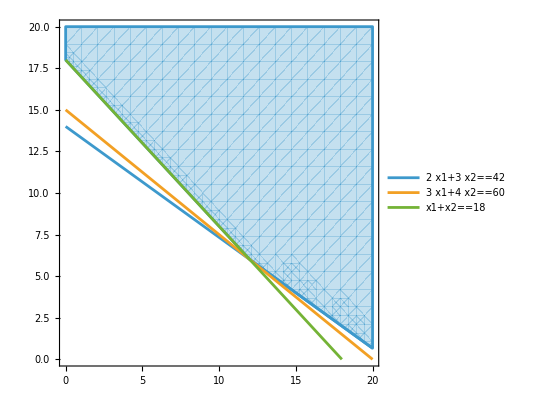

```mathematica
Show[rp,cp]
```

Ud fra vores skitse, kan vi se at bibetingelsen 3 x_1+4 x_2>=60 er overflødig. Den bidrager ikke med noget ny information, da den aldrig er aktiv alene. Denne kan vi altså med fordel smide væk, eftersom problemet ville være det samme, hvis denne ikke var der.

### (c)

Ved at gange objektivfunktionen med minus et, kan vi omdanne problemet fra et minimeringsproblem, til et maksimeringsproblem. Det samme kan vi gøre for bibetingelserne, så de passer i simplex algoritmen. Da bliver problemet

max -4 x_1-7 x_2
u.b.b
-2 x_1-3 x_2<=-42
-3 x_1-4 x_2<=-60
-x_1-x_2<=-18
x_1,x_2>=0

### (d)

Vi ser at objektiv koefficienterne alle er negative, hvormed de vil være positive, ligeså snart de kommer ind tableauet, og det vil ligne at vi befinder os i en optimal løsning med det samme. Derudover er (0,0) ikke inkluderet som en BFS, og dermed vil vi starte vores algoritme uden for mulighedsområdet, hvilket ikke vil virke for simplex algoritmen.

## Opgave 4: formulering af betingelser og simplex

### (a)

Vi definerer to beslutningsvariable, en for hver produkttype. 
x_1=mængde af produkttype 1
x_2=mængde af produkttype 2
Vi ved at profitten er givet ved 1 krone for produkt 1 og 2 kroner for produkt 2. Dermed bliver objektiv funktionen z=x_1+2 x_2 hvor z måler profit i kroner.

### (b) og (c)

Her ses en oversigt over rescourcebrug for de forskellige produkttyper, samt mængden er rescourcer til rådighed

Rescourceforbrug/Produkttype | x_1 | x_2 | Kapacitet
Rescource 1 | 1 | 3 | 200
Rescource 2 | 2 | 2 | 300

Derudover kan der maksimalt sælges 60 enheder af produkt 2. Da bliver bibetingelserne

x_1+3 x_2<=200
2 x_1+2 x_2<=300⟹x_1+x_2<=150
x_2<=60

### (d)

Vi får det samlede maksimeringsproblem

max x_1+2 x_2
u.b.b
x_1+3 x_2<=200
x_1+x_2<=150
x_2<=60
x_1,x_2>=0

Vi løser problemet med simplex.
Her ses tableauet

Vi løser med simplex

Her ses løsningstableuaet

Vi ser at den optimale værdi for objektivfunktionen er 175. Her produceres 125 enheder af x_1 og 25 enheder af x_2. Desuden ser vi at tredje bibetingelse ikke er aktiv.

## Opgave 5: simplex med opstillelse af problem

### (a)

For at opsætte modellen, starter vi med at danne os et overblik. Vi har beslutningsvariablene
bulk carrier =x_1->salgspris 120 mio. euro
RORO ship =x_2-> salgspris 200 mio. euro
container ship=x_3-> sallgspris 260 mio. euro
Vi laver desuden en oversigt over hvor rescourcebrug og kapacitet for de forskellige beslutningsvariable

Rescource/skipstype | x_1 | x_2 | x_3 | Kapacitet
B1: Docks | 1 | 1 | 1 | 11
B2: Labour | 30 | 15 | 45 | 300
B3: Kapital | 40 | 80 | 120 | 820

Man kan ikke producerer negative mængder, hvilket også indsættes i modellen. Dermed har vi følgende model

max 120 x_1+200 x_2+260 x_3
u.b.b
x_1+x_2+x_3<=11
30 x_1+15 x_2+45 x_3<=300
40 x_1+80 x_2+120 x_3<=820
x_1,x_2,x_3>=0

Vi har antaget at kan gange op i bibetinglser og salg uden at de påvirker mængden man benytter. Alt er altså perfekt skalerbart.  Vi har antaget at man ikke kan producere negative mængder. Vi har antaget divisibilitet og perfekt viden. Vi har antaget at både begrænsninger og objektivfunktionen bare er linearkombinationer. Vi har antaget at man godt kan bygge halve skibe (kontinuitet).

### (b)

Vi løser problemet med simplex. Her opstilles tableauet

Derefter gøres simplexalgoritmen

Da fås følgende løsningstableau

Vi ser at løsningen bliver når (x_1,x_2,x_3)=(1.5,9.5,0), og her bliver værdien af objektivfunktionen 2080.

## Ugeseddel 2: Dual simplex og sensitivitet

## Opgave 1: opstillelse af problem og løsning vha. simplex

### (a)

Vi starter med at opstille problemet

Max 20 x_1+30 x_2
u.b.b
2 x_1+x_2<=16
2 x_1+3 x_2<=24
2 x_1+6 x_2<=42

Ovenstående er netop en lineær model for problemet.

### (b)

Vi løser problemet ved brug af simplex metoden

-Graphics-

-Graphics-

Løsningen ses af sidste af de ovenstående screenshots

### (c)

Vi ser at skyggeprisen for første rescource er nul, eftersom denne ikke bliver benyttet, og virksomheden dermed heller ikke ville være villig til at betale for at få mere af denne på nuværende tidspunkt. Derudover ser vi at at skyggeprisen på rescource 2 er 10 kroner, da profitten ville blive øget med 10 kroner, hvis man får lov til at slække denne begrænsning. Vi ser at vi benytter hele vores mængde af rescource 3, men at skyggeprisen her alligevel er nul. Det betyder at profitten ikke ville stige, hvis man fik mere af denne rescoruce, også selvom man nu benytter hele sin beholdning af denne rescource.

## Opgave 2

Vi opskriver først problemet

Max              | 4 x_1+2 x_2+5 x_3
U.B.B | -5 x_1-4 x_2-3 x_3>=-11
  | 2 x_1+x_2+3 x_3=8
  | x_1,x_2,x_3>=0

Vi omskriver

-5 x_1-4 x_2-3 x_3>=-11⟹5 x_1+4 x_2+3 x_3<= 11
2 x_1+x_2+3 x_3=8⟹Piecewise[{{2 x_1+x_2+3 x_3>=8⟹-2 x_1-x_2-3 x_3<=-8, }, {2 x_1+x_2+3 x_3<=8, }}]

Dermed bliver problemet

Max              | 4 x_1+2 x_2+5 x_3
U.B.B | 5 x_1+4 x_2+3 x_3<= 11
  | -2 x_1-x_2-3 x_3<=-8
  | 2 x_1+x_2+3 x_3<=8
  | x_1,x_2,x_3>=0

Derefter løser vi problemet med simplex metoden

Skifter til primal simplex da en mulig løsning er x_1=x_2=0 og x_3=2.67

## Opgave 3 (omdan dual)

### (a)

Det dual program bliver

Min 5 y_1+7 y_2
u.b.b.
2 y_1+3 y_2>=42
3 y_1+4 y_2>=60
y_1+y_2>=18
y_1,y_2>=0

### (b)

For at opjektivfunktionens værdi skal blive 105 skal 5 y_1+7 y_2=105. Hvis vi sætter y_2=0 ser vi at y_1=21. Vi undersøger om dette er en mulig løsning

```mathematica
AT:=({{2, 3}, {3, 4}, {1, 1}});yv:=({{21}, {0}})
```

```mathematica
AT.yv
```

(42
63
21)

Vi ser altså at punktet opfylder alle bibetingelser og dermed må (y_1,y_2)=(21,0) være en mulig løsning. Stærk dualitet siger at objektivfunktionen til det primal program ikke kan antage en højere værdi en objektivfunktionen til det duale program, og dermed kan det primale program ikke have en løsning hvor værdien af objektivfunktionen er højere end 105.

### (c)

Vi løser det primale problem med simplex algoritmen og får følgende sluttableau

Vi ser at der er en optimal løsning når (x_1,x_2,x_3)=(1,1,0) og her bliver værdien af objektivfunktionen 102. Vi bemærker at x_3 ikke er med i basis, men at den har reduced cost lig 0 (se i z rækken). Det betyder at vi kan indrage denne i vores basis, uden at ændre på objektivfunktionens værdi, og der må altså være flere løsning. Eksempelvis kan vi lave en basis med x_3 og x_1 i stedet og få nedenstående løsningstableau

Eller vi kan skabe en basis med x_2 og x_3 og få følgende tableau

Hvilke alle er løsninger som giver samme objektivværdi.

Det duale problem har samme værdi af objektivkoefficienten, samtidigt med at (y_1,y_2)=(12,6).

### Opgave 4

(a) Sandt, dette skylde at antallet af slackvariable i det primale progblem vil være lig antallet af bibetingelser. Det betyder at det samlede antal variable (hvis man tæller slackvariable med) bliver antal strukturelle variable plus antal bibetingelser. 

I det dual problem vil antallet a strukturelle variable være lig antallet af bibetingelser fra det primale program, og antallet af bibetingelser vil være lig mængden af elementer i “c” vektoren. Dermed vil antallet af variable (med slackvariable talt med) være lig hinanden i de to problemer, svarende til at summen af variable og bibetingelser vil være det samme i de to problemer.

(b) Sandt. Løsningen til det primale problem står i b-vektoren og løsningen til det duale problem kan aflæses i z-rækken. 

(c) Falsk. Hvis det primale problem er ubegrænset, findes der ingen mulige løsninger til det duale program.

## Opgave 5: manual sensitivtetsanalyse med sluttableau

Vi starter med sensitivtetsanalyse af objektivkoefficienterne. 
x_3:
Denne variabel indgår ikke i basis, og dermed kan den tilhørende objektivkoefficient falde uendeligt, uden at dette ville inkludere den i basisen. Den tilladte stigning bestemmes af reduced cost for samme variabel, som bliver 30. Dermed kan x_3 koefficienten varierer i intervallet [-∞;80+30] = [-∞;110].

x_1:
Dette er en basisvariabel. Vi bemærker først at der både findes værdier i den tiilhørende række, som er større end nul og mindre end nul. Dermed bliver hverken den øvre eller den nedre grænse ∞. Vi finder maksimalt fald, ved at beregner ratiosne mellem værdierne i z-rækken og værdierne i x_1 rækken (dog uden første position i denne vektor, da det er pivotpositionen):

```mathematica
{30/(5/2),(80/3)/(2/3)}
```

{12,40}

Vi ser at den laveste af disse to er 12. Dermed bliver det tilladte fald for c_1=60 altså værdien 12. Den maksimale stigning er givet ved

```mathematica
-(10/3)/(-1/6)
```

20

Dermed bliver intervallet for denne objektivkoefficient [60-12;60+20] = [48;80].

x_2:

Denne variabel indgår heller ikke i basis, og der er både positive og negative værdier i rækken. Dermed bliver maksimal stigning

```mathematica
{-30/-1,-(-80/3)/(1/3)}
```

{30,80}

30, som er minimum af ovenstående ratios. Det maksimale fald bliver

```mathematica
10/3/(1/3)
```

10

dermed 10. Vi får følgende interval [40-10;40+30] = [30;70]